```mathematica
Get["D:\\faks 3. letnik\\matlab\\dn2\\mccPi.m"]
(*Generira naključne točke znotraj enotskega kroga in nato vrne približek in napako kot rezultat (znotraj kroga,če je razdalja od izhodišča manjša ali enaka 1)*)areaPi[n_]:=Module[{znotri=0,x,y,priblizekPija,napaka},
For[i=1,i<=n,i++,
x=RandomReal[];
y=RandomReal[];
If[(x^2+y^2)<=1,znotri++];];
priblizekPija=4*znotri/n;
napaka=Abs[priblizekPija-Pi];
{priblizekPija,napaka}]


(*Definira funkcijo calcPi, ki sprejme argument n*)
calcPi[n_]:=Module[{priblizekPija,napaka,Tnot,Tzuni},(*Uporablja lokalne spremenljivke znotraj funkcije*){priblizekPija,napaka}=areaPi[n];(*Predstavlja rezultat finkcije areaPi[n]*)
r=Sqrt[RandomReal[1,n]];(*Generiranje naključnih vrednosti radija za točke znotraj kroga*)
θ=RandomReal[{0,2 π},n];(*Generiranje naključnih vrednosti kota za točke znotraj kroga*)
Tnot=Transpose[{r Cos[θ],r Sin[θ]}];(*Točke znotraj kroga*)
xZunaj=RandomReal[{-1,1},n];(*Naključne točke po x*)
yZunaj=RandomReal[{-1,1},n];(*Naključne točke po y*)
rZunaj=Sqrt[xZunaj^2+yZunaj^2];(*Izračun razdalj od izhodišča (0,0) za točke zunaj kroga*)
Tzuni=Select[Transpose[{xZunaj,yZunaj}],Norm[#]>1&];(*Točke zunaj kroga*)
krog=Table[{Cos[t],Sin[t]},{t,0,2 π,0.01}];(*Seznam točk,ki predstavljajo krožnico,s korakom 0.01*)
Print["Približek za π: ",N[priblizekPija]];
Print["Napaka: ",N[napaka]];
(*Izris grafa točk znotraj in zunaj kroga*)(*Tooltip nam omogoča zapis v legendi Epilog pa nam omogoči dodajanje krožnice*);
ListPlot[{Tooltip[Tnot,"Znotraj kroga"],Tooltip[Tzuni,"Zunaj kroga"]},PlotStyle->{Red,Blue},AspectRatio->Automatic,PlotLabel->"Točke znotraj in zunaj kroga",Frame->True,FrameLabel->{"x","y"},Epilog->{Green,Line[krog]},PlotLegends->Placed[PointLegend[Automatic,{"Znotraj kroga","Zunaj kroga"},LegendMarkers->"Bubble"],{Right,Top}]]]
```

Približek za π: 3.14592

Napaka: 0.00432735

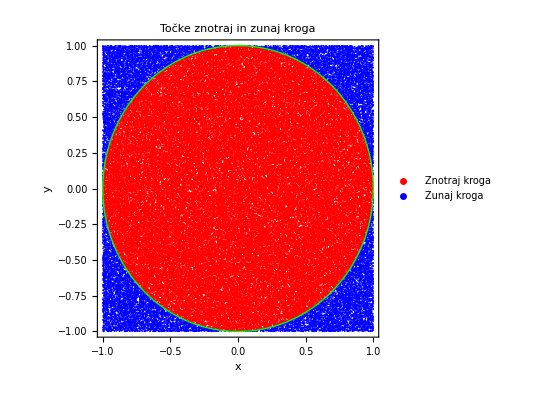

```mathematica
calcPi[100000]
```

# 2. del naloge Taylorjeva vrsta

```mathematica
(*f[t_] funkcija ki jo bomo uporabili za Taylorjevo vrsto , ki bo poleg vrste spremenljivka našega okolja(Module)*)
Manipulate[Module[{f,vrsta},f[t_]:=Sin[t]*t^2*Exp[-t];
vrsta=Normal[Series[f[t],{t,2,red}]];(*Izračun Taylorjeve vrste funkcije f[t]okoli točke 2 do željenega reda, ki ga določimo s parametrom red*)

(*Izris obeh funkcij na istem grafu in prikaz spreminjanja vrste glede na red, vidimo da večji kot bo red bolj se bo prilegala osnovni funkciji f[t]*)
Plot[{f[t],vrsta},{t,0,4},PlotLegends->{"f[t]",Row[{"Taylorjeva vrsta, red: ",red}]}]],{{red,4,"Red Taylorjeve vrste"},1,10,1}]
```